# PL/0 parser

References

- Introduction to the Theory of Computation, Michael Sipser	.
- Gate lectures by Ravindrababu Ravula: Compiler design.

Overview

This parser uses a finite automaton to recognize regular expressions which are also used by the lexical analyzer (lexer) to define the tokens to recognize. The input specified by the user is converted into a list of tokens and then is passed to the parser which builds a parse tree based on a given grammar. The grammar also has associated actions that are instructions that describe how to synthesize the tree into an intermediate code (IC) representation.

## Initialization

Finite state machine

### Deterministic finite automaton (DFA)

In the theory of computation, a branch of theoretical computer science, a deterministic finite automaton (DFA)—also known as deterministic finite acceptor (DFA), deterministic finite state machine (DFSM), or deterministic finite state automaton (DFSA)—is a finite-state machine that accepts or rejects strings of symbols and only produces a unique computation (or run) of the automaton for each input string.

DFAs recognize exactly the set of regular languages, which are, among other things, useful for doing lexical analysis and pattern matching. DFAs can be built from nondeterministic finite automata (NFAs) using the powerset construction method. This is useful because usually NFA are slower to compute.

```mathematica
Protect[ϵ]; (* ϵ will be used as a symbol to denote the empty string *)
Transition[parent_,child_,inputSymbol_]:=<|"Parent"->parent,"Node"->child,"InputSymbol"->inputSymbol|>;
EmptyTransition[parent_,child_]:=Transition[parent,child,ϵ];
FATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];
Concatenate[l_]:=Apply[Join,l];
```

```mathematica
NameTag[machine_Association,state_]:=Subscript[machine["Name"],ToString[state]];

Options[FiniteAutomataPlot]={"Legended"->True,"Labeled"->False};
FiniteAutomataPlot[machine_Association,OptionsPattern[]]:=Block[{graphData,startTag,acceptTags,legend,graph},
Switch[OptionValue["Labeled"],
True,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
,
False,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>p->n];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
];

legend = PointLegend[{LightBlue,Red,Green,Purple},{"State","Start state","Accept state","Start/Accept state"},LegendMarkers->Graphics[Disk[]]];

graph = Graph[
graphData,
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
];

If[OptionValue["Legended"],
Return[Legended[graph,legend]],
Return[graph]
]
];
```

```mathematica
(* DFA object constructor *)
DFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,(* Descriptive name to keep in track the regular operations applied to it *)
"Type"->"DFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept,
"StateExpressions"->stateExpr (* Each state may have an associated expression *)
|>;

(* Return every deterministic transition leading to state *)
DFATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];

(* Get the next state *)
Options[DFAIterate]={"Trace"->False};
DFAIterate[transitions_,state_,inputSymbol_,OptionsPattern[]]:=Block[{next},
next = Cases[
DFATransitions[transitions,state],
KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]
];

(* A DFA must have only one available transition *)
If[Length[next]==1,
If[OptionValue["Trace"],
Return[First[next]]
,
Return[First[next]["Node"]];
]
,
(* TODO: Crear mecanismo de alerta *)
Return[$Failed];
]
];

(* Returns the trace of the computation and the result of whether the machine accepts the inputString *)
DFACompute[machine_Association,inputString_]:=Block[{computation,result},
computation = FoldList[
DFAIterate[machine["Transitions"],#1["Node"],#2,"Trace"->True]&,
<|"Node"->machine["StartState"]|>,
inputString
];
result = MemberQ[machine["AcceptStates"],Last[computation]["Node"]];
Return[{computation,result}]
];
```

Plotting functions

```mathematica
Options[DFAPlotExecution] = {"SimpleNodes"->False};
DFAPlotExecution[machine_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags},
trace = DFACompute[machine,inputString];
executionSteps = Drop[First[trace],1];
ruleIndexes = Map[Position[machine["Transitions"],#]&,executionSteps];

If[OptionValue["SimpleNodes"],
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = machine["StartState"]->Red;
acceptTags = Map[#->Green&,machine["AcceptStates"]];
,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[machine,p]->NameTag[machine,n],i]];
startTag = NameTag[machine,machine["StartState"]]->Red;
acceptTags = Map[NameTag[machine,#]->Green&,machine["AcceptStates"]];
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{i->Green}]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

#### Examples

DFA declaration, where L(m_1) = {ω | ω contains at least one 1 and an even number of 0s follow the last 1}.

```mathematica
m1 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,3,{0}],
Transition[3,2,{0,1}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

Plot of m_1

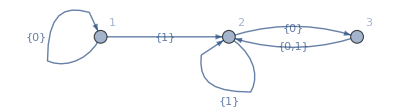

```mathematica
FiniteAutomataPlot[m1,"Labeled"->True]
```

Trace of the computation

```mathematica
DFACompute[m1,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},True}

Plot of the execution with 10100 as input

```mathematica
DFAPlotExecution[m1,{1,0,1,0,0}]
```

DFA declaration, where L(m_2) = {ω | ω ends in a 1}.

```mathematica
m2 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,1,{0}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

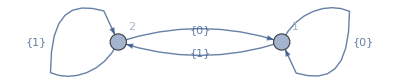

```mathematica
FiniteAutomataPlot[m2,"Labeled"->True]
```

```mathematica
DFACompute[m2,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→1,InputSymbol→{0}|>},False}

```mathematica
DFAPlotExecution[m2,{1,1,1,0,1}]
```

### Non-deterministic Finite Automata (NFA)

In automata theory, a finite state machine is called a deterministic finite automaton (DFA), if

each of its transitions is uniquely determined by its source state and input symbol, and
reading an input symbol is required for each state transition.
A nondeterministic finite automaton (NFA), or nondeterministic finite state machine, does not need to obey these restrictions. In particular, every DFA is also an NFA. Sometimes the term NFA is used in a narrower sense, referring to a NFA that is not a DFA, but not in this article.

Using the subset construction algorithm, each NFA can be translated to an equivalent DFA, i.e. a DFA recognizing the same formal language. Like DFAs, NFAs only recognize regular languages.

```mathematica
NFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,
"Type"->"NFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept ,
"StateExpressions"->stateExpr
|>;

ContainsQ[list_List,form_]:=MemberQ[list,form];
ContainsQ[form1_,form2_]:=(form1===form2);

PureNondetStateQ[transitions_,state_]:=(DeleteDuplicates[FATransitions[transitions,state][[All,"InputSymbol"]]] === {ϵ});

(* Return the list of nodes accesible via empty transitions *)
NFANondetNodes[transitions_,state_Association]:=Cases[FATransitions[transitions,state["Node"]],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_Integer]:=Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_List]:=DeleteDuplicates[Flatten[Map[NFANondetNodes[transitions,#]&,state]]];
NFANondetNodesRecursive[transitions_,states_] := FixedPoint[DeleteDuplicates[Join[#,NFANondetNodes[transitions,#[[All,"Node"]]]]]&,states];

Options[NFAIterate]={"Trace"->False};
NFAIterate[transitions_,state_?AtomQ,inputSymbol_,OptionsPattern[]]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
(* Get all the transitions corresponding to a DFA *)
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

(* Run through the empty transitions of the DFA nodes *)
forkTransitions = NFANondetNodes[transitions,deterministicNodes]; (* Get past the current deterministic nodes *)
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions]; (* Append every valid nondet transition *)

(* The next nodes will be a union between the deterministic transitions and the nodes reachable from nondet transitions *)
next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,
If[OptionValue["Trace"],
Return[next],
Return[next[[All,"Node"]]]
]
,
Return[{}]
];
];
NFAIterate[transitions_,state_List,inputSymbol_,opt:OptionsPattern[]]:=DeleteDuplicates[Flatten[Map[NFAIterate[transitions,#,inputSymbol,opt]&,state]]];

NFACompute[machine_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[
machine["Transitions"],
{<|"Node"->machine["StartState"]|>}
];
computation = FoldList[
NFAIterate[machine["Transitions"],#1[[All,"Node"]],#2,"Trace"->True]&,
start,
inputString
];
result = Apply[Or,Map[MemberQ[machine["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];
```

```mathematica
TransitionApplyThreshold[transition_,threshold_]:=MapAt[#+threshold&,transition,{{Key["Parent"]},{Key["Node"]}}];
MachineApplyThreshold[machine_Association,threshold_]:=<|
"Name"->machine["Name"],
"Transitions"->Map[TransitionApplyThreshold[#,threshold]&,machine["Transitions"]],
"StartState"->machine["StartState"]+threshold,
"AcceptStates"->machine["AcceptStates"]+threshold,
"StateExpressions"->If[Length[machine["StateExpressions"]]≠ 0,MapAt[#+threshold&,machine["StateExpressions"],{All,1}],{}]
|>;
```

```mathematica
GetDirectSuccesors[machine_,state_]:=Select[
Nest[NFANondetNodes[machine["Transitions"],#]&,{state},2],
(!ContainsQ[machine["AcceptStates"],#["Parent"]] &&PureNondetStateQ[machine["Transitions"],#["Parent"]] && Length[FAParents[machine["Transitions"],#["Parent"]]]==1)
&
];

ReplaceKey[assoc_,key_,replaceTo_]:=MapAt[replaceTo&,assoc,Key[key]];

DeleteIntermediateTransition[transitions_,startState_,endState_]:=Block[{deleteState,replacement,newTransitions,cleanedUp},
deleteState = endState["Parent"];
replacement = ReplaceKey[endState,"Parent",startState["Node"]];
cleanedUp = DeleteCases[transitions,KeyValuePattern["Parent"->deleteState]];
cleanedUp = DeleteCases[cleanedUp,KeyValuePattern["Node"->deleteState]];

newTransitions = Append[cleanedUp,replacement];
Return[newTransitions];
];

SimplifyStateIteration[nfa_,state_]:=Block[{newMachine,newTransitions},
newMachine = nfa;
newTransitions = Fold[
DeleteIntermediateTransition[#1,<|"Node"->state|>,#2]&,
nfa["Transitions"],
GetDirectSuccesors[nfa,state]
];
newMachine["Transitions"] = newTransitions;
Return[newMachine];
];
SimplifyState[nfa_,state_]:=FixedPoint[SimplifyStateIteration[#,state]&,nfa];

SimplifyMachine[nfa_]:=Block[{simplified,oldStates,newStates,stateRelabelRule = {}},
simplified = Fold[SimplifyState,nfa,GetStates[nfa["Transitions"]]];

oldStates = GetStates[simplified["Transitions"]];
newStates = Range[0,Length[oldStates]-1];
stateRelabelRule = Thread[oldStates->newStates];

simplified["Transitions"] = DeleteDuplicates[MapAt[Replace[#,stateRelabelRule]&,simplified["Transitions"],{{All,Key["Parent"]},{All,Key["Node"]}}]];
simplified["StartState"] = Replace[simplified["StartState"],stateRelabelRule];
simplified["AcceptStates"] = ReplaceAll[simplified["AcceptStates"],stateRelabelRule];
If[Length[simplified["StateExpressions"]]≠ 0,
simplified["StateExpressions"] = MapAt[Replace[#,stateRelabelRule]&,simplified["StateExpressions"],{All,1}];
];
Return[simplified];
];
```

```mathematica
NFAUnion[machine1_Association,machine2_Association]:=Block[{minIndex,newIndexThreshold,newM1,newM2,newAccept,newTransitions,newMachine,newStateExpressions},
minIndex = Min[machine1["Transitions"][[All,"Parent"]]];
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM1 = MachineApplyThreshold[machine1,1];
newM2 = MachineApplyThreshold[machine2,newIndexThreshold+1];
newAccept = Sort[Join[newM1["AcceptStates"],newM2["AcceptStates"]]];
newTransitions = {EmptyTransition[minIndex,newM1["StartState"]], EmptyTransition[minIndex,newM2["StartState"]]};
newStateExpressions = SortBy[Join[newM1["StateExpressions"],newM2["StateExpressions"]],First];

newMachine = <|
"Name"->StringJoin[machine1["Name"],"∪",machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[newM1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAUnion[machines__/;Length[List[machines]]>2]:=Fold[NFAUnion,First[List[machines]],Rest[List[machines]]];
```

```mathematica
NFAConcatention[machine1_Association,machine2_Association]:=Block[{newIndexThreshold,newM2,newTransitions,newMachine,newStateExpressions},
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM2 = MachineApplyThreshold[machine2,newIndexThreshold];

newTransitions = Map[EmptyTransition[#,newM2["StartState"]]&,machine1["AcceptStates"]];

newStateExpressions = Join[machine1["StateExpressions"],newM2["StateExpressions"]];
newStateExpressions = If[Length[newStateExpressions]≠ 0,SortBy[Join[machine1["StateExpressions"],newM2["StateExpressions"]],First],{}];

newMachine = <|
"Name"->StringJoin[machine1["Name"],machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[machine1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->machine1["StartState"],
"AcceptStates"->newM2["AcceptStates"],
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAConcatention[machines__/;Length[List[machines]]>2]:=Fold[NFAConcatention,First[List[machines]],Rest[List[machines]]];
```

```mathematica
NFAStar[machine_Association]:=Block[{minIndex,newM,newTransitions,newAccept,newMachine},
minIndex = Min[machine["Transitions"][[All,"Parent"]]];
newM = MachineApplyThreshold[machine,1];
newTransitions = Join[{EmptyTransition[minIndex,newM["StartState"]]},Map[EmptyTransition[#,newM["StartState"]]&,newM["AcceptStates"]]];
newAccept = Append[newM["AcceptStates"],minIndex];

newMachine = <|
"Name"->StringJoin["(",machine["Name"],")^*"],
"Type"->"NFA",
"Transitions"->Join[newM["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newM["StateExpressions"]
|>;
Return[newMachine];
];
```

```mathematica
(* Check if there is at least one of the accepted states in searchState *)
ContainsStateQ[stateList_,searchState_?AtomQ]:=MemberQ[stateList,searchState];
ContainsStateQ[stateList_,searchState_List]:=Apply[Or,Map[MemberQ[stateList,#]&,searchState]];

(* Get parents of the current state *)
FAParents[transitions_,state_]:=DeleteDuplicates[Cases[transitions,KeyValuePattern[{"Node"->state}]][[All,"Parent"]]];

(* Check if the state is inaccesible *)
JunkStateQ[transitions_,start_,state_]:=Block[{stateParents,nonSelfTransitions},
If[ContainsStateQ[start,state],Return[False]];
stateParents = FAParents[transitions,state];
nonSelfTransitions = Complement[stateParents,{state}];
If[Length[nonSelfTransitions]==0,
Return[True],
Return[False]
]
];

SafeSort[l_List]:=Sort[l];
SafeSort[l_?AtomQ]:=l;

(* Infer the alphabet from the transition list *)
GetAlphabet[transitions_]:=DeleteCases[DeleteDuplicates[Flatten[transitions[[All,"InputSymbol"]]]],ϵ];

(* Infer the states from the transition list *)
GetStates[transitions_]:=Sort[DeleteDuplicates[Flatten[Cases[transitions,KeyValuePattern[{"Parent"->p_,"Node"->n_}]:>{p,n}]]]];

(* Get the states reachable from the current states list *)
Explore[transitions_,states_]:=Map[
Transition[
SafeSort[states],
SafeSort[DeleteDuplicates[NFAIterate[transitions,states,#,"Trace"->False]]],
{#}]&,
GetAlphabet[transitions]
];

(* Explore one step down each branch of the computation and append it to the explored branches list *)
StepDown[transitions_,branches_]:=DeleteDuplicates[
Flatten[
Join[
branches,
Map[
Explore[
transitions,
#["Node"]
]&,
branches
]
],
1]
];

NewStateNode[node_,newStateRules_]:=
<|
"Parent"->Replace[node["Parent"],newStateRules],
"Node"->Replace[node["Node"],newStateRules],
"InputSymbol"->node["InputSymbol"]
|>;

NFAToDFA[machine_Association]:=Block[{protoDFA,start,protoDFAStates,newStateRules,newStates,containsAccept,newMachine,newAccept,newStart,newTransitions,newTransitionsCleanedUp,protoDFAExpressionNodes,newStateExpressionsNodes},
If[machine["Type"] =!= "NFA",Return[$Failed]];

(* Explore all paths until there is no unexplored transition *)
start = 
FixedPoint[
DeleteDuplicates[
Join[
#,
NFANondetNodes[machine["Transitions"],#[[All,"Node"]]]]
]&,
{<|"Node"->machine["StartState"]|>}
];

(* Make a DFA by exploring all possible paths in the NFA *)
protoDFA = FixedPoint[StepDown[machine["Transitions"],#]&,{<|"Node"->start[[All,"Node"]]|>}];
protoDFAStates = DeleteDuplicates[Join[Drop[protoDFA,1][[All,"Parent"]],Drop[protoDFA,1][[All,"Node"]]]];

(* Match old NFA parameters to the new DFA *)
newStateRules = Thread[protoDFAStates->Range[Length[protoDFAStates]]];
newStates =newStateRules[[All,2]];
containsAccept = Position[protoDFAStates,s_/;ContainsStateQ[s,machine["AcceptStates"]]];
newAccept = Extract[newStates,containsAccept];
newStart = Replace[First[protoDFAStates],newStateRules];
newTransitions = Map[NewStateNode[#,newStateRules]&,Drop[protoDFA,1]];
newTransitionsCleanedUp = DeleteDuplicates[DeleteCases[newTransitions,t_/; JunkStateQ[newTransitions,newStart,t["Node"]]]];

protoDFAExpressionNodes = Concatenate[
Map[
Thread[Cases[protoDFAStates,s_/;ContainsStateQ[s,First[#]]]->Last[#]]&,
machine["StateExpressions"]
]
];
If[Length[protoDFAExpressionNodes]≠0,
newStateExpressionsNodes = MapAt[Replace[#,newStateRules]&,protoDFAExpressionNodes,{All,1}]
,
newStateExpressionsNodes = {}
];

newMachine = <|
"Name"->machine["Name"],
"Type"->"DFA",
"Transitions"->newTransitionsCleanedUp,
"StartState"->newStart,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressionsNodes
|>;
Return[newMachine];
];
```

Plotting functions

```mathematica
(* Pretty output for NFAExecutionTree *)
GenerationTransform[node_Association,generation_]:={
StringJoin["G: ",ToString[generation-1]," S: ",ToString[node["Parent"]]]->StringJoin["G: ",ToString[generation]," S: ",ToString[node["Node"]]]
,
ToString[node["InputSymbol"]]
};
GenerationTransform[nodes_List,generation_]:=Map[GenerationTransform[#,generation]&,nodes];

NFAReplaceParents[transitions_,newParent_]:=Map[MapAt[newParent&,#,Key["Parent"]]&,transitions];

NFAExecutionTreeIterate[transitions_,state_?AtomQ,inputSymbol_]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

forkTransitions = NFANondetNodes[transitions,deterministicNodes];
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions];
forkTransitions = NFAReplaceParents[forkTransitions,state]; (* This is the only difference from NFAIterate *)

next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,Return[next],Return[{}]];
];
NFAExecutionTreeIterate[transitions_,state_List,inputSymbol_]:=DeleteDuplicates[Flatten[Map[NFAExecutionTreeIterate[transitions,#,inputSymbol]&,state]]];

NFAExecutionTreeComputeTrace[machine_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[machine["Transitions"],{<|"Node"->machine["StartState"]|>}]; (* This is the only difference from NFACompute *)
computation = FoldList[NFAExecutionTreeIterate[machine["Transitions"],#1[[All,"Node"]],#2]&,start,inputString];
result = Apply[Or,Map[MemberQ[machine["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];

(* Plot the execution tree showing the active states at every input *)
NFAExecutionTree[machine_Association,inputString_]:=Block[{trace,root,traceTree},
trace = Drop[First[NFAExecutionTreeComputeTrace[machine,inputString]],1];
root = First[GenerationTransform[First[trace],1]];
traceTree = Flatten[MapIndexed[GenerationTransform[#1,First[#2]]&,trace],1];

TreePlot[
DeleteDuplicates[traceTree],
Automatic,StringJoin["G: 0 S: ",ToString[machine["StartState"]]],

VertexLabeling->True,
DirectedEdges->True
]
];

Options[NFAPlotExecution] = {"SimpleNodes"->False};
NFAPlotExecution[machine_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags,currentStates,start,parentStates},
trace = NFACompute[machine,inputString];
executionSteps = First[trace];
ruleIndexes = Map[Position[machine["Transitions"],Apply[Alternatives,#]]&,executionSteps];
currentStates = Cases[machine["Transitions"],KeyValuePattern[{"Node"->n_}]:>n];
parentStates = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_}]:>p];
start = DeleteDuplicates[Sort[Join[{<|"Node"->machine["StartState"]|>},NFANondetNodes[machine["Transitions"],machine["StartState"]]]]];

If[OptionValue["SimpleNodes"],
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
acceptTags = Map[#->Green&,machine["AcceptStates"]];
startTag = machine["StartState"]->Red;
,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[machine,p]->NameTag[machine,n],i]];
acceptTags = Map[NameTag[machine,#]->Green&,machine["AcceptStates"]];
startTag = NameTag[machine,machine["StartState"]]->Red;
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{(i-1)->Green}]}],
Row[{"Start states: ",Sort[start[[All,"Node"]]]}],
Row[{"Parent states: ",Sort[Extract[parentStates,ruleIndexes[[i]]]]}],
Row[{"Current states: ",Sort[Extract[currentStates,ruleIndexes[[i]]]]}],
Row[{"Accept states: ",machine["AcceptStates"]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

#### Examples

NFA declaration, where L(n_1) = {ω | ω contains either 101 or 11 as a substring}.

```mathematica
n1 = NFA[
"q",
{
Transition[1,1,{0,1}],
Transition[1,2,{1}],
Transition[2,3,{0,ϵ}],
Transition[3,4,{1}],
Transition[4,4,{0,1}]
},
1,
{4}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0,1}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0,ϵ}|>,<|Parent→3,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→4,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{4},StateExpressions→{}|>

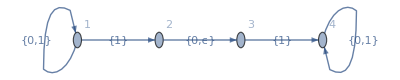

```mathematica
FAPlot[n1,"Labeled"->True]
```

```mathematica
Column@First[NFACompute[n1,{0,1,0,1,1,0}]][[All,All,"Node"]]
```

{1}
{1}
{1,2,3}
{1,3}
{1,2,3,4}
{1,2,3,4,4}
{1,3,4}

```mathematica
NFAPlotExecution[n1,{0,1,0,1,1,0}]
```

NFA declaration, where L(nfa) = 0 Σ^*1.

```mathematica
nfa = NFA[
"q",
{
Transition[0,1,{0}],
EmptyTransition[1,2],
EmptyTransition[1,3],
Transition[2,4,{1}],
EmptyTransition[4,1],
Transition[3,5,{0}],
EmptyTransition[5,1],
EmptyTransition[4,6],
EmptyTransition[5,6],
Transition[6,7,{1}]
},
0,
{7}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→5,InputSymbol→{0}|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{1}|>},StartState→0,AcceptStates→{7},StateExpressions→{}|>

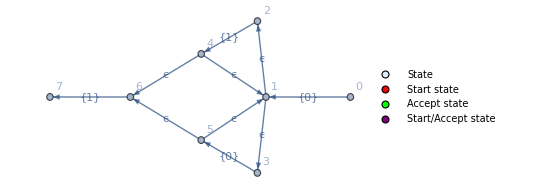

```mathematica
FAPlot[nfa,"Labeled"->True]
```

```mathematica
NFAPlotExecution[nfa,{0,0,1,1,1}]
```

Union operation

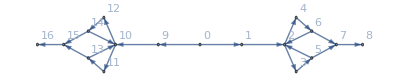

```mathematica
FAPlot@NFAUnion[nfa,nfa]
```

#### Applications

This automata recongnizes a

```mathematica
aNFA = NFA["a",{Transition[0,1,{"a"}]},0,{1}]
```

<|Name→a,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{a}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

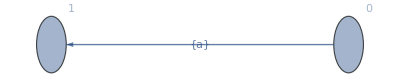

```mathematica
FAPlot[aNFA,"Labeled"->True]
```

and this one recognizes b

```mathematica
bNFA = NFA["b",{Transition[0,1,{"b"}]},0,{1}]
```

<|Name→b,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{b}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

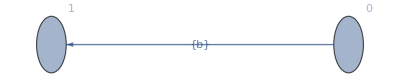

```mathematica
FAPlot[bNFA,"Labeled"->True]
```

The union of both, that is a ∪ b is represented by the NFA

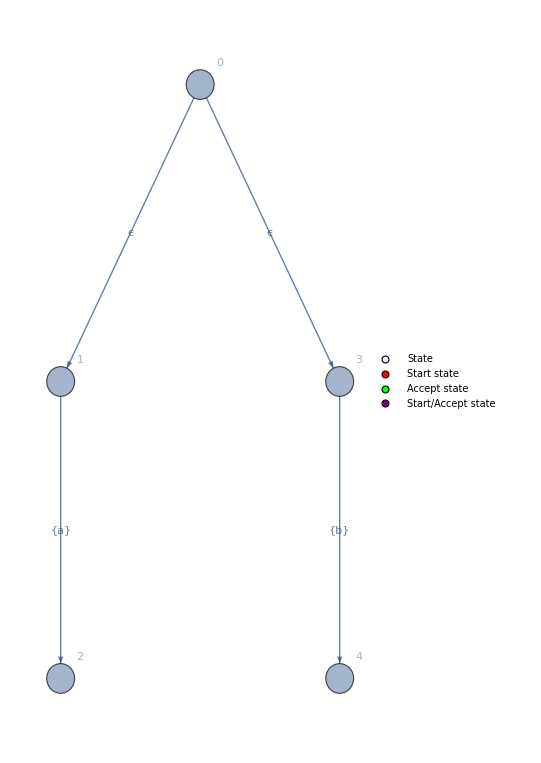

```mathematica
FAPlot[NFAUnion[aNFA,bNFA],"Labeled"->True]
```

Using various operations we can recognize (a ∪ (b))^*aba

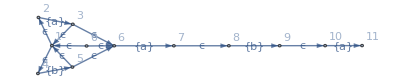

```mathematica
FAPlot[NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA],"Labeled"->True]
```

```mathematica
example = NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA]
```

<|Name→(a∪b)^*aba,Type→NFA,Transitions→{<|Parent→2,Node→3,InputSymbol→{a}|>,<|Parent→4,Node→5,InputSymbol→{b}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→4,InputSymbol→ϵ|>,<|Parent→0,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→1,InputSymbol→ϵ|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{a}|>,<|Parent→3,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→0,Node→6,InputSymbol→ϵ|>,<|Parent→8,Node→9,InputSymbol→{b}|>,<|Parent→7,Node→8,InputSymbol→ϵ|>,<|Parent→10,Node→11,InputSymbol→{a}|>,<|Parent→9,Node→10,InputSymbol→ϵ|>},StartState→0,AcceptStates→{11},StateExpressions→{}|>

```mathematica
NFAPlotExecution[example,{"a","b","b","a","b","a"}]
```

```mathematica
NFAPlotExecution[example,{"a","b","b","a","b","b"}]
```

Regular expressions

A regular expression, regex or regexp  is a sequence of characters that define a search pattern. Usually this pattern is used by string searching algorithms for “find” or “find and replace” operations on strings, or for input validation. It is a technique that developed in theoretical computer science and formal language theory.

```mathematica
RegexUnion[args__]:=NFAUnion[args];
RegexConcatenation[args__]:=NFAConcatention[args];
RegexStar[machine_Association]:=NFAStar[machine];
RegexStar[c_String]:=NFAStar[Regex[c]];
RegexDagger[machine_Association]:=NFAConcatention[machine,NFAStar[machine]];
RegexDagger[c_String]:=NFAConcatention[Regex[c],NFAStar[Regex[c]]];
```

```mathematica
Regex[c_String/;StringLength[c]==1]:=NFA[c,{Transition[0,1,{c}]},0,{1}];
Regex[c_String/;StringLength[c]==1,stateExpr_]:=NFA[c,{Transition[0,1,{c}]},0,{1},{1->stateExpr}];
Regex[s_String/;StringLength[s]>1,tokenRecognize_:""]:=Block[{m},
m =Apply[NFAConcatention,Map[Regex,Characters[s]]];
If[tokenRecognize≠ "",
m["StateExpressions"] =Thread[m["AcceptStates"]->tokenRecognize];
];

Return[m];
];
Regex[r_Association,tokenRecognize_]:=Block[{m = r},
m["StateExpressions"] = Thread[m["AcceptStates"]->tokenRecognize];
Return[m];
];
```

```mathematica
RegexAlphabet[alphabet_]:=Block[{input,name,transitions,acceptStates,newMachine},
input = Characters[alphabet];
newMachine = <|
"Name"->StringJoin[Riffle[input,"∪"]],
"Type"->"NFA",
"Transitions"->Map[Transition[0,#,{input[[#]]}]&,Range[Length[input]]],
"StartState"->0,
"AcceptStates"->Range[Length[input]],
"StateExpressions"->{}
|>;
Return[newMachine];
];

RegexAlphabetLowercase[]:=RegexAlphabet[StringJoin@Alphabet[]];
RegexAlphabetUppercase[]:=RegexAlphabet[StringJoin@ToUpperCase[Alphabet[]]];
RegexAlphabet[]:=RegexAlphabet[StringJoin@Join[Alphabet[],ToUpperCase[Alphabet[]]]];
RegexDigits[]:=RegexAlphabet[StringJoin@Map[ToString,Range[0,9]]];

asciiChars = {"\t","\n","\f","\r"," ","!","#","$","%","&","'","(",")","*","+",",","-",".","/","0","1","2","3","4","5","6","7","8","9",":",";","<","=",">","?","@","A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z","[","\\","]","^","_","`","a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z","{","|","}","~",".7f"};

RegexASCIIChars[]:=RegexAlphabet[StringJoin@asciiChars];
```

```mathematica
RegexCompute[machine_,input_]:=Block[{trace,result,recognizedTokens},
If[machine["Type"]== "NFA",
{trace,result} = NFACompute[machine,Characters[input]];
recognizedTokens = 
Cases[
Last[trace][[All,"Node"]],
(node_ /; ContainsQ[machine["StateExpressions"][[All,1]],node]):> Replace[node,machine["StateExpressions"]]
];

,
{trace,result} =DFACompute[machine,Characters[input]];
recognizedTokens = 
Cases[
{Last[trace]["Node"]},
(node_ /; ContainsQ[machine["StateExpressions"][[All,1]],node]):> Replace[node,machine["StateExpressions"]]
];
];

Return[{trace,result,recognizedTokens}];
];
```

Lexer

In computer science, lexical analysis, lexing or tokenization is the process of converting a sequence of characters (such as in a computer program or web page) into a sequence of tokens (strings with an assigned and thus identified meaning). A program that performs lexical analysis may be termed a lexer, tokenizer, or scanner, though scanner is also a term for the first stage of a lexer.

```mathematica
Token[symbol_String,name_String]:=<|"Class"->"Token","Symbol"->symbol,"Name"->name|>;
CreateTokens[list_]:=Map[Token[#[[1]],#[[2]]]&,list];
```

```mathematica
TokenKeyword[symbol_String,name_String]:=<|"Class"->"TokenKeyword","Symbol"->symbol,"Name"->name|>;
CreateTokenKeywords[list_]:=Map[TokenKeyword[#[[1]],#[[2]]]&,list];
```

```mathematica
GetToken[input_,symbolTokens_,keywordTokens_]:=Block[{symbolAccept,symbolResult,keywordAccept,keywordResult},
{symbolAccept,symbolResult} = Rest[RegexCompute[symbolTokens,input]];
{keywordAccept,keywordResult} = Quiet[Rest[RegexCompute[keywordTokens,input]]];
If[keywordAccept,Return[First[keywordResult]]];
If[symbolAccept,Return[First[symbolResult]]];
Return["Nothing"];
];

SafeStringTake[string_,n_]:=StringTake[string,Min[n,StringLength[string]]];
SafeStringTake[string_,{m_,n_}]:=StringTake[string,{m,Min[n,StringLength[string]]}];

GetNextToken[program_,symbolTokens_,keywordTokens_]:=Block[{tokenizerResult,nextToken},
(* Try to get the first biggest token from the input *)
tokenizerResult = NestWhileList[
{
First[#]+1,
GetToken[SafeStringTake[program,First[#]+1],symbolTokens,keywordTokens]
}&,
{
0,
None
},
((Last[#]=!= "Nothing")&&(First[#]≤StringLength[program]))&
];

nextToken = If[Length[tokenizerResult]>2,tokenizerResult[[-2]],Last[tokenizerResult]];
Return[nextToken];
];

SafeMod[m_,0]:=m;
SafeMod[m_,n_]:=Mod[m,n];
LinePosition[pos_,lineBreaks_]:=SafeMod[pos,Last[Select[Prepend[lineBreaks+1, 0],#≤pos&]]];
ColumnPosition[pos_,lineBreaks_]:=Position[Ordering[Prepend[lineBreaks, pos]],1][[1,1]]-1;

Tokenize[program_,symbolTokens_,keywordTokens_]:=Block[
{
length,type,
cursor = 0,
tokenList = {},
omitTokens = {"Whitespace","LineBreak"},
formattedTokens
},

(* Iterate over all the input getting the tokens one by one *)
While[cursor<StringLength[program],
{length,type} = GetNextToken[StringDrop[program,cursor],symbolTokens,keywordTokens];
If[!MemberQ[omitTokens,type],AppendTo[tokenList,<|"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>]];
cursor+=length;
];

(* Tokens without value only carry type information *)
formattedTokens = Map[
If[#["Type"] =!=#["Value"],
<|
"Type"->#["Type"],
"Value"->#["Value"]
|>,
<|
"Type"->#["Type"]
|>
]
&,
tokenList
];

Return[formattedTokens];
];
```

### Example

A lexer for simple arithmetic parser

```mathematica
arithmeticTokenSymbols = CreateTokens[
{
{" ","Whitespace"},
{"*", "*"},
{"+", "+"},
{"(", "("},
{")", ")"}
}
];
arithmeticTokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,arithmeticTokenSymbols]]];
arithmeticTokenSymbolsDFA = NFAToDFA[arithmeticTokenSymbolsNFA];
idLiteral = Regex[NFAToDFA[RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]]],"id"];
```

```mathematica
tokens = Tokenize["5+6*(7+9)",arithmeticTokenSymbolsDFA,idLiteral]
```

{<|Type→id,Value→5|>,<|Type→+|>,<|Type→id,Value→6|>,<|Type→*|>,<|Type→(|>,<|Type→id,Value→7|>,<|Type→+|>,<|Type→id,Value→9|>,<|Type→)|>}

Parser

Parsing, syntax analysis, or syntactic analysis is the process of analysing a string of symbols, either in natural language, computer languages or data structures, conforming to the rules of a formal grammar. A parser is a software component that takes input data (frequently text) and builds a data structure – often some kind of parse tree, abstract syntax tree or other hierarchical structure, giving a structural representation of the input while checking for correct syntax.

In this project a recursive descent parser is used.  A recursive descent parser is a kind of top-down parser built from a set of mutually recursive procedures (or a non-recursive equivalent) where each such procedure implements one of the nonterminals of the grammar. Thus the structure of the resulting program closely mirrors that of the grammar it recognizes.

### Rule matching

```mathematica
Protect[EmptyString,Term,NonTerm];

GetArgument[_[arg_]]:=arg;
Substitute[l1_,l2_]:=Join[l1,Drop[l2,Length[l1]]];

TermMatchQ[input_,{}]:=True;
TermMatchQ[input_,terms_]:=(Take[input,Length[terms]][[All,"Type"]] == Map[GetArgument,terms]);
GenerateTransition[rule_,stateId_,lastId_]:=MapIndexed[{rule["From"],stateId}->{#1,lastId+First[#2]}&,rule["To"]];

MatchTerminalsWithRule[stateId_,lastId_,input_,rule_]:=Block[{terms,transition,rest,cuttedInput,currentState,lastIndex,matchTransitions},

currentState = rule["From"];
If[rule["To"]===EmptyString[],Return[{{{currentState,stateId}->{EmptyString[],lastId+1}},{},input,lastId+1}]];

transition = GenerateTransition[rule,stateId,lastId];
lastIndex = Last@Last@Last@transition;
terms = TakeWhile[rule["To"],Head[#]=!=NonTerm&];
rest = Drop[transition[[All,2]],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[TermMatchQ[input,terms],
matchTransitions =MapIndexed[
If[KeyExistsQ[#1,"Value"],
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2],#1["Value"]},
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2]}
]&,
Take[input,Length[terms]]
];
transition = Substitute[matchTransitions,transition];

cuttedInput = Drop[input,Length[terms]];
Return[{transition,rest,cuttedInput,lastIndex}];
,
Return[$Failed];
];
];

MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MatchTerminals[{state_,stateId_},lastId_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[{#,MatchTerminalsWithRule[stateId,lastId,input,#]}&,possibleTransitions,Last[#]=!=$Failed&]];
Return[matched];
];
```

#### Example

Given a simple arithmetic grammar

```mathematica
arithmeticGrammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString[]|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString[]|>
};
```

and the input i+i

```mathematica
testInput = Map[<|"Type"->#|>&,{"i","+","i"}]
```

{<|Type→i|>,<|Type→+|>,<|Type→i|>}

If we try to match with the rule E’ -> + i E’ since i can’t match with + the function will return false.

```mathematica
MatchTerminalsWithRule[1,4,testInput,<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>]
```

$Failed

If we try to match with the rule E -> i E’ V it will list the full transition,

```mathematica
{transition,rest,cuttedInput,lastIndex} = MatchTerminalsWithRule[1,4,testInput,<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>];
```

```mathematica
transition
```

{{NonTerm[E],1}→{Term[i],5},{NonTerm[E],1}→{NonTerm[E'],6},{NonTerm[E],1}→{NonTerm[V],7}}

the unmatched symbols of the rule,

```mathematica
rest
```

{{NonTerm[E'],6},{NonTerm[V],7}}

the remaining input

```mathematica
cuttedInput
```

{<|Type→+|>,<|Type→i|>}

and the last index used by the counter.

```mathematica
lastIndex
```

7

We can try with all the rules in the grammar at once and choose the first  rule that matches.

```mathematica
MatchTerminals[{NonTerm["E"],1},4,testInput,arithmeticGrammar]
```

{<|From→NonTerm[E],To→{Term[i],NonTerm[E'],NonTerm[V]}|>,{{{NonTerm[E],1}→{Term[i],5},{NonTerm[E],1}→{NonTerm[E'],6},{NonTerm[E],1}→{NonTerm[V],7}},{{NonTerm[E'],6},{NonTerm[V],7}},{<|Type→+|>,<|Type→i|>},7}}

### Parser

```mathematica
Protect[$IncompleteGrammar];
VerifyGrammar[grammar_]:=Block[{grammarKeys},
grammarKeys = DeleteDuplicates[Map[Keys,grammar]];
If[grammarKeys=={{"From","To","Action"}}, Return[True]];
If[MemberQ[grammarKeys, {"From","To"}], Return[$IncompleteGrammar]];
Return[False];
];
VerifyInput[input_]:=Block[{inputKeys},
(* Input must be a list of tokens with Type and Value entries. *)
inputKeys = DeleteDuplicates[Map[Keys,tokens]];
If[inputKeys == {{"Type","Value"}}, 
Return[True],
Return[False]
];
];

Options[Parse]={"Trace"->False};
Parse::incompleteGrammar = "Actions in this grammar are not correctly specified";
Parse::badGrammar = "Incorrect grammar";
Parse::badInput = "Incorrect input";
Parse[input_,grammar_,OptionsPattern[]]:=Block[{grammarCheck,pGrammar,trace,symbolRules,rule,stack,transitions,next,inputBuffer,lastId,parseTree,parseSymbol,toStack},
(* Error check *)
grammarCheck = VerifyGrammar[grammar];
If[grammarCheck == False,
Message[Parse::badGrammar];
Abort[];
];
If[grammarCheck ===$IncompleteGrammar,Message[Parse::incompleteGrammar]];
If[VerifyInput[input] == False,
Message[Parse::badInput];
Abort[];
];

(* Initialization *)
pGrammar = MapAt[NonTerm,grammar,{All,Key["From"]}];
stack = {};
parseTree = {};
lastId = 1;
inputBuffer = input;
parseSymbol = {First[pGrammar]["From"],1};
symbolRules = {};
trace = {<|"ParseSymbol"->parseSymbol,"Stack"->stack,"LastID"->lastId,"InputBuffer"->inputBuffer|>};

(* Loop until there are no input symbols left and no symbol left to parse *)
While[{inputBuffer,parseSymbol} =!= {{},None},
If[Head[First[parseSymbol]] ===NonTerm,

(* Case where the parse symbol is a non terminal *)
{rule,{transitions,next,inputBuffer,lastId} } = MatchTerminals[parseSymbol,lastId,inputBuffer,pGrammar];
AppendTo[parseTree,transitions];
AppendTo[symbolRules,{parseSymbol,rule["Action"]}];
,
(* Case where the parse symbol is a terminal *)
If[GetArgument[First[parseSymbol]] == First[inputBuffer]["Type"],
inputBuffer =Drop[inputBuffer,1];
next = {};
];
];

If[Length[next]>0,
(* If there are symbols left to process, process the first and push the rest to the stack *)
{parseSymbol,toStack}={First[next],Reverse[Rest[next]]};
stack = Join[stack,toStack];
,
(* If there are no symbols left, pop one from the stack *)
If[Length[stack] > 0,
{parseSymbol,stack}={Last[stack],Drop[stack,-1]};
,
(* Flag to stop the loop when the stack is empty *)
parseSymbol = None;
];
];

AppendTo[trace,<|"ParseSymbol"->parseSymbol,"Stack"->stack,"LastID"->lastId,"InputBuffer"->inputBuffer|>]
];

parseTree = Flatten[parseTree,1];

If[OptionValue["Trace"],
Return[trace],

If[grammarCheck ===$IncompleteGrammar,
Return[parseTree]
,
Return[{parseTree,symbolRules}]
]
];
];

Parse[input_,grammar_,symbolTokens_,keywordTokens_,opt:OptionsPattern[]]:=Parse[Tokenize[input,symbolTokens,keywordTokens],grammar,opt];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction,styledParseTree,styleRules},
parseTree = First@Parse[input,grammar];
styleRules = {NonTerm[x_]:>Style["NonTerm("<>ToString[x]<>")",Blue],Term[x_]:>Style["Term("<>ToString[x]<>")",Red]};
styledParseTree = ReplaceAll[parseTree,styleRules];
startProduction = First[First[styledParseTree]];
TreePlot[styledParseTree,Automatic,startProduction,VertexLabeling->True,AspectRatio->1/4]
];
```

Grammar beautification

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];

GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle]
];
```

#### Example

We can build a parse tree from the arithmetic grammar.

```mathematica
arithmeticGrammar = {
<|"From"->"E","To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->"V","To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->"V","To"->EmptyString[]|>,
<|"From"->"E'","To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->"E'","To"->EmptyString[]|>
};
```

```mathematica
GrammarPrettify[arithmeticGrammar]
```

E→{i,E',V}
V→{j,V}
V→EmptyString[]
E'→{+,i,E'}
E'→EmptyString[]

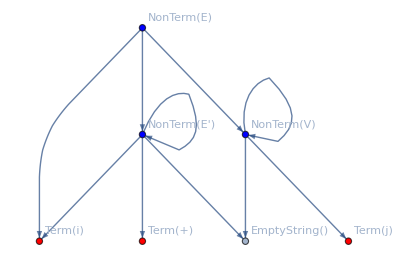

```mathematica
GrammarGraph[arithmeticGrammar]
```

```mathematica
testInput = Map[<|"Type"->#|>&,{"i","+","i"}];
```

Since no actions are specified in this grammar, a warning is given about the grammar being incomplete.

```mathematica
Parse[testInput,arithmeticGrammar]
```

Parse::incompleteGrammar: Actions in this grammar are not correctly specified

{{NonTerm[E],1}→{Term[i],2},{NonTerm[E],1}→{NonTerm[E'],3},{NonTerm[E],1}→{NonTerm[V],4},{NonTerm[E'],3}→{Term[+],5},{NonTerm[E'],3}→{Term[i],6},{NonTerm[E'],3}→{NonTerm[E'],7},{NonTerm[E'],7}→{EmptyString[],8},{NonTerm[V],4}→{EmptyString[],9}}

## PL/0 Implementation

Lexer tokens definition

Here we define the tokens that will be recognized by the lexer.

```mathematica
tokenSymbols = CreateTokens[
{
{" ","Whitespace"},
{"\n", "LineBreak"},
{":", "IncompleteAssign"},
{":=", "Assign"},
{"*", "Times"},
{"/", "Slash"},
{"+", "Plus"},
{"-", "Minus"},
{"=", "Equal"},
{"#", "NotEqual"},
{"(", "LeftParenthesis"},
{")", "RightParenthesis"},
{";", "Semicolon"},
{",", "Comma"},
{".", "Dot"},
{">", "Greater"},
{">=", "GreaterOrEqual"},
{"<", "Lower"},
{"<=", "LowerOrEqual"}
}
];

tokenIdentifiersAndLiterals = CreateTokens[
{
{"identifier", "Identifier"},
{"number", "Number"}
}
];

tokenKeywords = CreateTokenKeywords[
{
{"const", "Const"},
{"var", "Var"},
{"procedure", "Procedure"},
{"call", "Call"},
{"print", "Print"},
{"begin", "Begin"},
{"end", "End"},
{"if", "If"},
{"then", "Then"},
{"while", "While"},
{"do", "Do"},
{"odd", "Odd"}
}
];
```

```mathematica
tokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenSymbols]]];
tokenSymbolsDFA = NFAToDFA[tokenSymbolsNFA];

identifierRegex =RegexConcatenation[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]];
numberLiteral = RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]];

identifierRegex = Regex[identifierRegex,"Identifier"];
integerLiteral = Regex[numberLiteral,"NumberLiteral"];
symbolRecognizer= RegexUnion[identifierRegex,integerLiteral,tokenSymbolsDFA];
```

```mathematica
keywordNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenKeywords]]];
keywordRecognizer = NFAToDFA[keywordNFA];
```

#### Example

```mathematica
testProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end.";
```

```mathematica
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
```

```mathematica
Dataset[tokens]
```

Dataset[<>]

Grammar definition

Here we define the PL/0 grammar in BNF form.

```mathematica
(* Variable name generator *)
currentVar = None;
index = 0;

ResetVarGenerator[]:=(index = 0);
NewVar[]:=(currentVar = StringJoin["$",ToString[index++]]);
CurrentVar[]:=currentVar;
CurrentVar[s_]:=StringJoin[s,currentVar];

LineJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""]," "]];
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
```

```mathematica
grammar = {
(* Program *)
<|"From"->"Program","To"->{NonTerm["Block"],Term["Dot"]},
"Action"->{"TACode":>ColumnJoin[{NonTerm["Block"]["TACode"],"halt"}]}|>,
<|"From"->"Block","To"->{NonTerm["ConstOpt"],NonTerm["VarOpt"],NonTerm["ProcRep"],NonTerm["Statement"]},
"Action"->{
"Value":>"",
"TACode":>ColumnJoin[
{
NonTerm["ConstOpt"]["TACode"],
NonTerm["VarOpt"]["TACode"],
NonTerm["ProcRep"]["TACode"],
NonTerm["Statement"]["TACode"]
}
]
}|>,

<|"From"->"ConstOpt","To"->{Term["Const"],Term["Identifier"],Term["Equal"],Term["NumberLiteral"],NonTerm["ConstOptRep"],Term["Semicolon"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"declare_const",Term["Identifier"]["Value"],Term["NumberLiteral"]["Value"]}]
}
|>,
<|"From"->"ConstOpt","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"ConstOptRep","To"->{Term["Comma"], Term["Identifier"],Term["Equal"],Term["NumberLiteral"],NonTerm["ConstOptRep"]},
"Action"->{
"TACode":>ColumnJoin[
{
LineJoin[{"declare_const",Term["Identifier"]["Value"],Term["NumberLiteral"]["Value"]}],
NonTerm["ConstOptRep"]["TACode"]
}
]
}
|>,
<|"From"->"ConstOptRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"VarOpt","To"->{Term["Var"],Term["Identifier"],NonTerm["VarOptRep"],Term["Semicolon"]},
"Action"->{
"Value":>"",
"TACode":>ColumnJoin[
{
LineJoin[{"declare_var",Term["Identifier"]["Value"]}],
NonTerm["VarOptRep"]["TACode"]
}
]
}|>,
<|"From"->"VarOpt","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"VarOptRep","To"->{Term["Comma"], Term["Identifier"],NonTerm["VarOptRep"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"declare_var",Term["Identifier"]["Value"]}]
}
|>,
<|"From"->"VarOptRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"ProcRep","To"->{Term["Procedure"],Term["Identifier"],Term["Semicolon"],NonTerm["Block"],Term["Semicolon"],NonTerm["ProcRep"]},
"Action"->{
"Value":>Term["Identifier"]["Value"],
"TACode":>
ColumnJoin[
{
LineJoin[{"begin_proc",Term["Identifier"]["Value"]}],
NonTerm["Block"]["TACode"],
LineJoin[{"end_proc",Term["Identifier"]["Value"]}],
NonTerm["ProcRep"]["TACode"]
}
]
}|>,
<|"From"->"ProcRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

(* Statements *)
<|"From"->"Statement","To"->{Term["Identifier"],Term["Assign"],NonTerm["Expression"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Expression"]["TACode"],
LineJoin[{"set",Term["Identifier"]["Value"],NonTerm["Expression"]["Value"]}]
}
]
}|>,
<|"From"->"Statement","To"->{Term["Call"],Term["Identifier"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"call", Term["Identifier"]["Value"]}]
}|>,
<|"From"->"Statement","To"->{Term["Print"],Term["Identifier"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"print", Term["Identifier"]["Value"]}]
}|>,
<|"From"->"Statement","To"->{Term["Begin"],NonTerm["Statement"],NonTerm["StatementRep"],Term["End"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Statement"]["TACode"],
NonTerm["StatementRep"]["TACode"]
}
]
}|>,
<|"From"->"Statement","To"->{Term["If"],NonTerm["Condition"],Term["Then"],NonTerm["Statement"]},
"Action"->{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Condition"]["TACode"],
LineJoin[{"if_false",NonTerm["Condition"]["Value"],"goto",CurrentVar["L"]}],
NonTerm["Statement"]["TACode"],
LineJoin[{"label",CurrentVar["L"]}]
}
]
}|>,
<|"From"->"Statement","To"->{Term["While"],NonTerm["Condition"],Term["Do"],NonTerm["Statement"]},
"Action"->{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
LineJoin[{"label",CurrentVar["L1"]}],
NonTerm["Condition"]["TACode"],
LineJoin[{"if_false",NonTerm["Condition"]["Value"],"goto",CurrentVar["L2"]}],
NonTerm["Statement"]["TACode"],
LineJoin[{"goto",CurrentVar["L1"]}],
LineJoin[{"label",CurrentVar["L2"]}]
}
]
}|>,
<|"From"->"Statement","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"StatementRep","To"->{Term["Semicolon"],NonTerm["Statement"],NonTerm["StatementRep"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Statement"]["TACode"],
NonTerm["StatementRep"]["TACode"]
}
]
}|>,
<|"From"->"StatementRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

(* Conditionals *)
<|"From"->"Condition","To"->{Term["Odd"],NonTerm["Expression"]},
"Action"->{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Expression"]["TACode"],
LineJoin[{"odd",NonTerm["Expression"]["Value"],CurrentVar[]}]
}
]
}
|>,
<|"From"->"Condition","To"->{NonTerm["Expression1"],NonTerm["Op"],NonTerm["Expression2"]},"Action"->{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Expression1"]["TACode"],
NonTerm["Expression2"]["TACode"],
LineJoin[{NonTerm["Op"]["Value"],NonTerm["Expression1"]["Value"], NonTerm["Expression2"]["Value"],CurrentVar[]}]
}
]
}|>,
<|"From"->"Expression1","To"->{NonTerm["Expression"]},"Action"->{"Value":>NonTerm["Expression"]["Value"],"TACode":>NonTerm["Expression"]["TACode"]}|>,
<|"From"->"Expression2","To"->{NonTerm["Expression"]},"Action"->{"Value":>NonTerm["Expression"]["Value"],"TACode":>NonTerm["Expression"]["TACode"]}|>,
<|"From"->"Op","To"->{Term["Equal"]},"Action"->{"Value"->"equal"}|>,
<|"From"->"Op","To"->{Term["NotEqual"]},"Action"->{"Value"->"not_equal"}|>,
<|"From"->"Op","To"->{Term["Lower"]},"Action"->{"Value"->"less"}|>,
<|"From"->"Op","To"->{Term["LowerOrEqual"]},"Action"->{"Value"->"less_or_equal"}|>,
<|"From"->"Op","To"->{Term["Greater"]},"Action"->{"Value"->"greater"}|>,
<|"From"->"Op","To"->{Term["GreaterOrEqual"]},"Action"->{"Value"->"greater_or_equal"}|>,

(* Numeric expressions *)
<|"From"->"Expression","To"->{NonTerm["SignOpt"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":>If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],NonTerm["SignOpt"]["Value"], NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"],CurrentVar[]}]
}
]
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"]
}
]
|>,

<|"From"->"SignOpt","To"->{Term["Plus"]},
"Action"->{"Value"->"+"}|>,
<|"From"->"SignOpt","To"->{Term["Minus"]},
"Action"->{"Value"->"-"}|>,
<|"From"->"SignOpt","To"->EmptyString[],
"Action"->{"Value"->""}|>,

<|"From"->"AddRep","To"->{Term["Plus"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":>If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"],CurrentVar[]}]
}
],
"Op"->"add"
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"],
"Op"->"add"
}
]
|>,

<|"From"->"AddRep","To"->{Term["Minus"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":> If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"],CurrentVar[]}]
}
],
"Op"->"substract"
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"],
"Op"->"substract"
}
]
|>,

<|"From"->"AddRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->"","Op"->""}|>,

<|"From"->"Term","To"->{NonTerm["Factor"],NonTerm["MultRep"]},
"Action":> If[NonTerm["MultRep"]["Value"] ≠"" ,
(* Case when there is a nonempty MultRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"],NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"],CurrentVar[]}]
}
]
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"]
}
]
|>,

<|"From"->"MultRep","To"->{Term["Times"],NonTerm["Factor"],NonTerm["MultRep"]},
"Action":>If[NonTerm["MultRep"]["Value"] ≠"" ,
(* Case when there is a nonempty MultRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"], NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"],CurrentVar[]}]
}
],
"Op"->"multiply"
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"],
"Op"->"multiply"
}
]
|>,

<|"From"->"MultRep","To"->{Term["Slash"],NonTerm["Factor"],NonTerm["MultRep"]},
"Action":>If[NonTerm["MultRep"]["Value"] ≠"" ,
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"], NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"],CurrentVar[]}]
}
],
"Op"->"divide"
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"],
"Op"->"divide"
}
]
|>,

<|"From"->"MultRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->"","Op"->""}|>,

<|"From"->"Factor","To"->{Term["Identifier"]},
"Action"->{"Value"->Term["Identifier"]["Value"],"TACode"->""}|>,

<|"From"->"Factor","To"->{Term["NumberLiteral"]},
"Action"->{"Value"->Term["NumberLiteral"]["Value"],"TACode"->""}|>,

<|"From"->"Factor","To"->{Term["LeftParenthesis"],NonTerm["Expression"],Term["RightParenthesis"]},
"Action"->{"Value"->NonTerm["Expression"]["Value"],"TACode"->NonTerm["Expression"]["TACode"]}|>
};
```

#### Example

```mathematica
GrammarPrettify[grammar]
```

Program→{Block,Dot}
Block→{ConstOpt,VarOpt,ProcRep,Statement}
ConstOpt→{Const,Identifier,Equal,NumberLiteral,ConstOptRep,Semicolon}
ConstOpt→EmptyString[]
ConstOptRep→{Comma,Identifier,Equal,NumberLiteral,ConstOptRep}
ConstOptRep→EmptyString[]
VarOpt→{Var,Identifier,VarOptRep,Semicolon}
VarOpt→EmptyString[]
VarOptRep→{Comma,Identifier,VarOptRep}
VarOptRep→EmptyString[]
ProcRep→{Procedure,Identifier,Semicolon,Block,Semicolon,ProcRep}
ProcRep→EmptyString[]
Statement→{Identifier,Assign,Expression}
Statement→{Call,Identifier}
Statement→{Print,Identifier}
Statement→{Begin,Statement,StatementRep,End}
Statement→{If,Condition,Then,Statement}
Statement→{While,Condition,Do,Statement}
Statement→EmptyString[]
StatementRep→{Semicolon,Statement,StatementRep}
StatementRep→EmptyString[]
Condition→{Odd,Expression}
Condition→{Expression,Op,Expression}
Op→{Equal}
Op→{NotEqual}
Op→{Lower}
Op→{LowerOrEqual}
Op→{Greater}
Op→{GreaterOrEqual}
Expression→{SignOpt,Term,AddRep}
SignOpt→{Plus}
SignOpt→{Minus}
SignOpt→EmptyString[]
AddRep→{Plus,Term,AddRep}
AddRep→{Minus,Term,AddRep}
AddRep→EmptyString[]
Term→{Factor,MultRep}
MultRep→{Times,Factor,MultRep}
MultRep→{Slash,Factor,MultRep}
MultRep→EmptyString[]
Factor→{Identifier}
Factor→{NumberLiteral}
Factor→{LeftParenthesis,Expression,RightParenthesis}

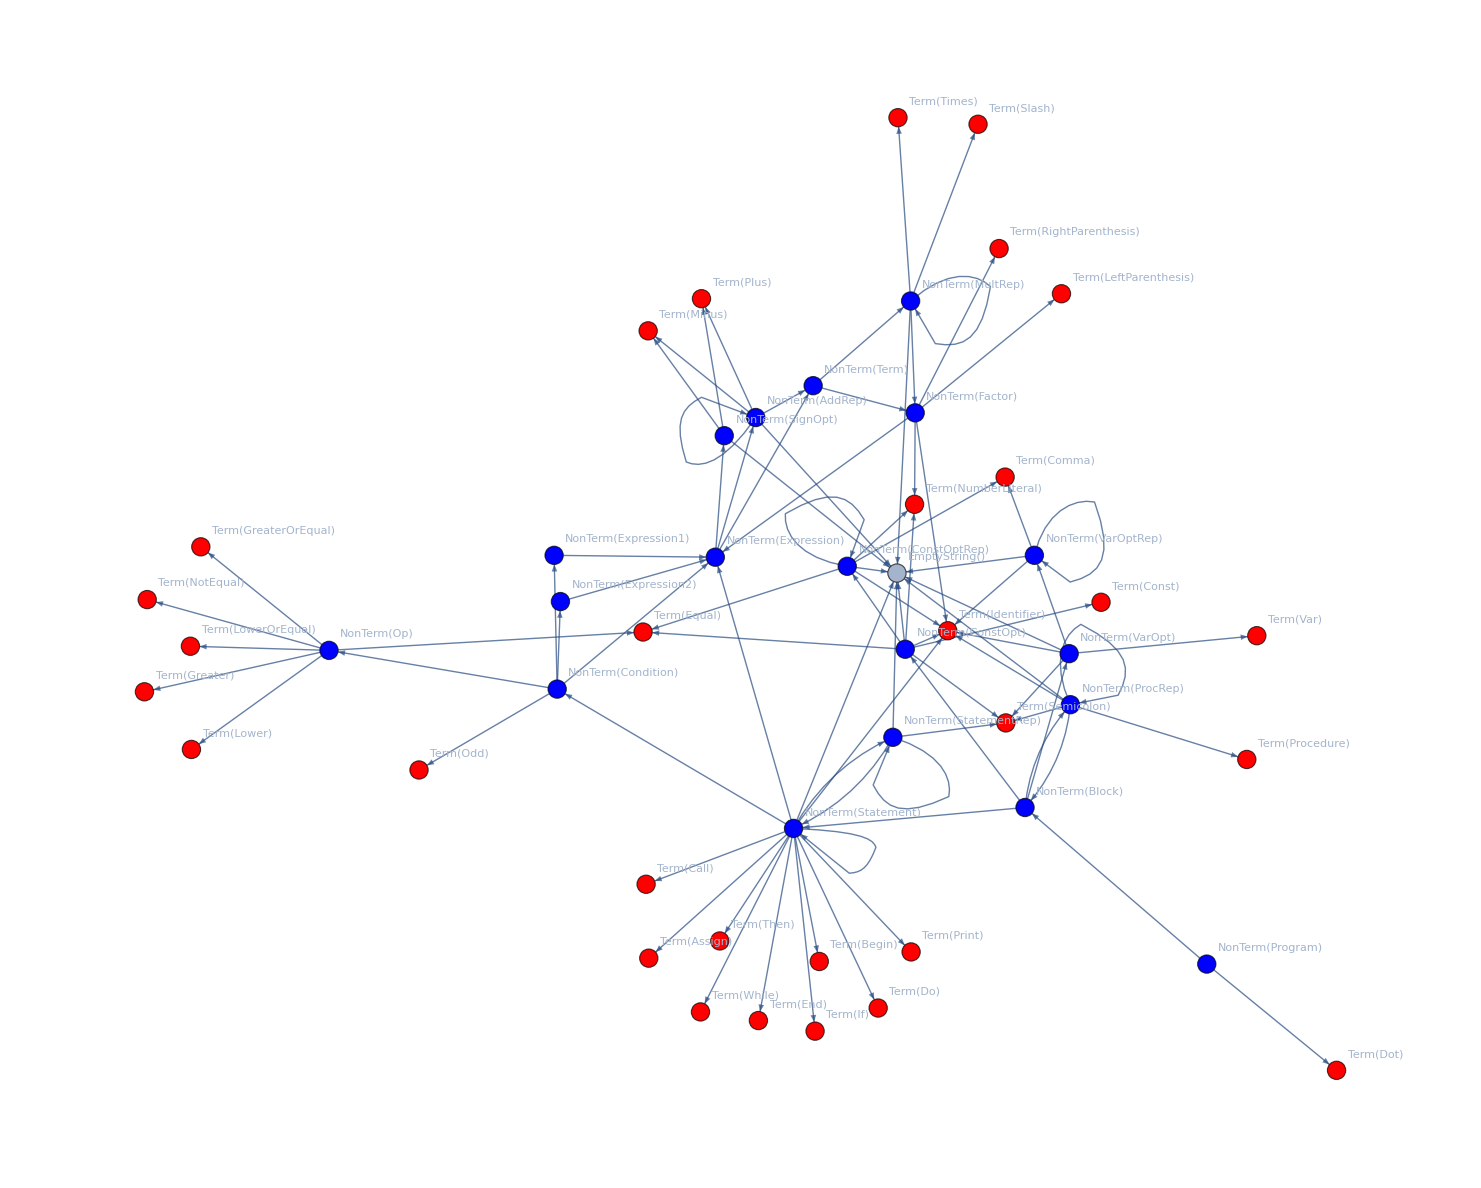

```mathematica
GrammarGraph[grammar]
```

```mathematica
testProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end.";
```

```mathematica
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
```

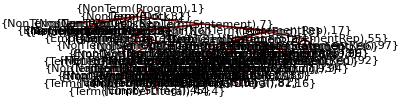

```mathematica
ParseTree[tokens,grammar]
```

```mathematica
Dataset@Parse[tokens,grammar,"Trace"->True]
```

Dataset[<>]

```mathematica
parseTree = Parse[tokens,grammar]
```

{{{NonTerm[Program],1}→{NonTerm[Block],2},{NonTerm[Program],1}→{Term[Dot],3},{NonTerm[Block],2}→{NonTerm[ConstOpt],4},{NonTerm[Block],2}→{NonTerm[VarOpt],5},{NonTerm[Block],2}→{NonTerm[ProcRep],6},{NonTerm[Block],2}→{NonTerm[Statement],7},{NonTerm[ConstOpt],4}→{EmptyString[],8},{NonTerm[VarOpt],5}→{Term[Var],9,var},{NonTerm[VarOpt],5}→{Term[Identifier],10,n},{NonTerm[VarOpt],5}→{NonTerm[VarOptRep],11},{NonTerm[VarOpt],5}→{Term[Semicolon],12},{NonTerm[VarOptRep],11}→{EmptyString[],13},{NonTerm[ProcRep],6}→{EmptyString[],14},{NonTerm[Statement],7}→{Term[Begin],15,begin},{NonTerm[Statement],7}→{NonTerm[Statement],16},{NonTerm[Statement],7}→{NonTerm[StatementRep],17},{NonTerm[Statement],7}→{Term[End],18},{NonTerm[Statement],16}→{Term[Identifier],19,n},{NonTerm[Statement],16}→{Term[Assign],20,:=},{NonTerm[Statement],16}→{NonTerm[Expression],21},{NonTerm[Expression],21}→{NonTerm[SignOpt],22},{NonTerm[Expression],21}→{NonTerm[Term],23},{NonTerm[Expression],21}→{NonTerm[AddRep],24},{NonTerm[SignOpt],22}→{EmptyString[],25},{NonTerm[Term],23}→{NonTerm[Factor],26},{NonTerm[Term],23}→{NonTerm[MultRep],27},{NonTerm[Factor],26}→{Term[LeftParenthesis],28,(},{NonTerm[Factor],26}→{NonTerm[Expression],29},{NonTerm[Factor],26}→{Term[RightParenthesis],30},{NonTerm[Expression],29}→{NonTerm[SignOpt],31},{NonTerm[Expression],29}→{NonTerm[Term],32},{NonTerm[Expression],29}→{NonTerm[AddRep],33},{NonTerm[SignOpt],31}→{EmptyString[],34},{NonTerm[Term],32}→{NonTerm[Factor],35},{NonTerm[Term],32}→{NonTerm[MultRep],36},{NonTerm[Factor],35}→{Term[NumberLiteral],37,1},{NonTerm[MultRep],36}→{EmptyString[],38},{NonTerm[AddRep],33}→{Term[Plus],39,+},{NonTerm[AddRep],33}→{NonTerm[Term],40},{NonTerm[AddRep],33}→{NonTerm[AddRep],41},{NonTerm[Term],40}→{NonTerm[Factor],42},{NonTerm[Term],40}→{NonTerm[MultRep],43},{NonTerm[Factor],42}→{Term[NumberLiteral],44,4},{NonTerm[MultRep],43}→{EmptyString[],45},{NonTerm[AddRep],41}→{EmptyString[],46},{NonTerm[MultRep],27}→{Term[Times],47,*},{NonTerm[MultRep],27}→{NonTerm[Factor],48},{NonTerm[MultRep],27}→{NonTerm[MultRep],49},{NonTerm[Factor],48}→{Term[NumberLiteral],50,5},{NonTerm[MultRep],49}→{EmptyString[],51},{NonTerm[AddRep],24}→{EmptyString[],52},{NonTerm[StatementRep],17}→{Term[Semicolon],53,;},{NonTerm[StatementRep],17}→{NonTerm[Statement],54},{NonTerm[StatementRep],17}→{NonTerm[StatementRep],55},{NonTerm[Statement],54}→{Term[If],56,if},{NonTerm[Statement],54}→{NonTerm[Condition],57},{NonTerm[Statement],54}→{Term[Then],58},{NonTerm[Statement],54}→{NonTerm[Statement],59},{NonTerm[Condition],57}→{NonTerm[Expression1],60},{NonTerm[Condition],57}→{NonTerm[Op],61},{NonTerm[Condition],57}→{NonTerm[Expression2],62},{NonTerm[Expression1],60}→{NonTerm[Expression],63},{NonTerm[Expression],63}→{NonTerm[SignOpt],64},{NonTerm[Expression],63}→{NonTerm[Term],65},{NonTerm[Expression],63}→{NonTerm[AddRep],66},{NonTerm[SignOpt],64}→{EmptyString[],67},{NonTerm[Term],65}→{NonTerm[Factor],68},{NonTerm[Term],65}→{NonTerm[MultRep],69},{NonTerm[Factor],68}→{Term[Identifier],70,n},{NonTerm[MultRep],69}→{EmptyString[],71},{NonTerm[AddRep],66}→{EmptyString[],72},{NonTerm[Op],61}→{Term[NotEqual],73,#},{NonTerm[Expression2],62}→{NonTerm[Expression],74},{NonTerm[Expression],74}→{NonTerm[SignOpt],75},{NonTerm[Expression],74}→{NonTerm[Term],76},{NonTerm[Expression],74}→{NonTerm[AddRep],77},{NonTerm[SignOpt],75}→{EmptyString[],78},{NonTerm[Term],76}→{NonTerm[Factor],79},{NonTerm[Term],76}→{NonTerm[MultRep],80},{NonTerm[Factor],79}→{Term[NumberLiteral],81,16},{NonTerm[MultRep],80}→{EmptyString[],82},{NonTerm[AddRep],77}→{EmptyString[],83},{NonTerm[Statement],59}→{Term[Begin],84,begin},{NonTerm[Statement],59}→{NonTerm[Statement],85},{NonTerm[Statement],59}→{NonTerm[StatementRep],86},{NonTerm[Statement],59}→{Term[End],87},{NonTerm[Statement],85}→{Term[Print],88,print},{NonTerm[Statement],85}→{Term[Identifier],89,n},{NonTerm[StatementRep],86}→{Term[Semicolon],90,;},{NonTerm[StatementRep],86}→{NonTerm[Statement],91},{NonTerm[StatementRep],86}→{NonTerm[StatementRep],92},{NonTerm[Statement],91}→{EmptyString[],93},{NonTerm[StatementRep],92}→{EmptyString[],94},{NonTerm[StatementRep],55}→{Term[Semicolon],95,;},{NonTerm[StatementRep],55}→{NonTerm[Statement],96},{NonTerm[StatementRep],55}→{NonTerm[StatementRep],97},{NonTerm[Statement],96}→{EmptyString[],98},{NonTerm[StatementRep],97}→{EmptyString[],99}},{{{NonTerm[Program],1},{TACode:>ColumnJoin[{NonTerm[Block][TACode],halt}]}},{{NonTerm[Block],2},{Value:>,TACode:>ColumnJoin[{NonTerm[ConstOpt][TACode],NonTerm[VarOpt][TACode],NonTerm[ProcRep][TACode],NonTerm[Statement][TACode]}]}},{{NonTerm[ConstOpt],4},{Value→,TACode→}},{{NonTerm[VarOpt],5},{Value:>,TACode:>ColumnJoin[{LineJoin[{declare_var,Term[Identifier][Value]}],NonTerm[VarOptRep][TACode]}]}},{{NonTerm[VarOptRep],11},{Value→,TACode→}},{{NonTerm[ProcRep],6},{Value→,TACode→}},{{NonTerm[Statement],7},{Value:>,TACode:>ColumnJoin[{NonTerm[Statement][TACode],NonTerm[StatementRep][TACode]}]}},{{NonTerm[Statement],16},{Value:>,TACode:>ColumnJoin[{NonTerm[Expression][TACode],LineJoin[{set,Term[Identifier][Value],NonTerm[Expression][Value]}]}]}},{{NonTerm[Expression],21},If[NonTerm[AddRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Term][TACode],NonTerm[AddRep][TACode],LineJoin[{NonTerm[AddRep][Op],NonTerm[SignOpt][Value],NonTerm[Term][Value],NonTerm[AddRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Term][Value],TACode:>NonTerm[Term][TACode]}]},{{NonTerm[SignOpt],22},{Value→}},{{NonTerm[Term],23},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode]}]},{{NonTerm[Factor],26},{Value→NonTerm[Expression][Value],TACode→NonTerm[Expression][TACode]}},{{NonTerm[Expression],29},If[NonTerm[AddRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Term][TACode],NonTerm[AddRep][TACode],LineJoin[{NonTerm[AddRep][Op],NonTerm[SignOpt][Value],NonTerm[Term][Value],NonTerm[AddRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Term][Value],TACode:>NonTerm[Term][TACode]}]},{{NonTerm[SignOpt],31},{Value→}},{{NonTerm[Term],32},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode]}]},{{NonTerm[Factor],35},{Value→Term[NumberLiteral][Value],TACode→}},{{NonTerm[MultRep],36},{Value→,TACode→,Op→}},{{NonTerm[AddRep],33},If[NonTerm[AddRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Term][TACode],NonTerm[AddRep][TACode],LineJoin[{NonTerm[AddRep][Op],NonTerm[Term][Value],NonTerm[AddRep][Value],CurrentVar[]}]}],Op→add},{Value:>NonTerm[Term][Value],TACode:>NonTerm[Term][TACode],Op→add}]},{{NonTerm[Term],40},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode]}]},{{NonTerm[Factor],42},{Value→Term[NumberLiteral][Value],TACode→}},{{NonTerm[MultRep],43},{Value→,TACode→,Op→}},{{NonTerm[AddRep],41},{Value→,TACode→,Op→}},{{NonTerm[MultRep],27},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}],Op→multiply},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode],Op→multiply}]},{{NonTerm[Factor],48},{Value→Term[NumberLiteral][Value],TACode→}},{{NonTerm[MultRep],49},{Value→,TACode→,Op→}},{{NonTerm[AddRep],24},{Value→,TACode→,Op→}},{{NonTerm[StatementRep],17},{Value:>,TACode:>ColumnJoin[{NonTerm[Statement][TACode],NonTerm[StatementRep][TACode]}]}},{{NonTerm[Statement],54},{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Condition][TACode],LineJoin[{if_false,NonTerm[Condition][Value],goto,CurrentVar[L]}],NonTerm[Statement][TACode],LineJoin[{label,CurrentVar[L]}]}]}},{{NonTerm[Condition],57},{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Expression1][TACode],NonTerm[Expression2][TACode],LineJoin[{NonTerm[Op][Value],NonTerm[Expression1][Value],NonTerm[Expression2][Value],CurrentVar[]}]}]}},{{NonTerm[Expression1],60},{Value:>NonTerm[Expression][Value],TACode:>NonTerm[Expression][TACode]}},{{NonTerm[Expression],63},If[NonTerm[AddRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Term][TACode],NonTerm[AddRep][TACode],LineJoin[{NonTerm[AddRep][Op],NonTerm[SignOpt][Value],NonTerm[Term][Value],NonTerm[AddRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Term][Value],TACode:>NonTerm[Term][TACode]}]},{{NonTerm[SignOpt],64},{Value→}},{{NonTerm[Term],65},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode]}]},{{NonTerm[Factor],68},{Value→Term[Identifier][Value],TACode→}},{{NonTerm[MultRep],69},{Value→,TACode→,Op→}},{{NonTerm[AddRep],66},{Value→,TACode→,Op→}},{{NonTerm[Op],61},{Value→not_equal}},{{NonTerm[Expression2],62},{Value:>NonTerm[Expression][Value],TACode:>NonTerm[Expression][TACode]}},{{NonTerm[Expression],74},If[NonTerm[AddRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Term][TACode],NonTerm[AddRep][TACode],LineJoin[{NonTerm[AddRep][Op],NonTerm[SignOpt][Value],NonTerm[Term][Value],NonTerm[AddRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Term][Value],TACode:>NonTerm[Term][TACode]}]},{{NonTerm[SignOpt],75},{Value→}},{{NonTerm[Term],76},If[NonTerm[MultRep][Value]≠,{Value:>NewVar[],TACode:>ColumnJoin[{NonTerm[Factor][TACode],NonTerm[MultRep][TACode],LineJoin[{NonTerm[MultRep][Op],NonTerm[Factor][Value],NonTerm[MultRep][Value],CurrentVar[]}]}]},{Value:>NonTerm[Factor][Value],TACode:>NonTerm[Factor][TACode]}]},{{NonTerm[Factor],79},{Value→Term[NumberLiteral][Value],TACode→}},{{NonTerm[MultRep],80},{Value→,TACode→,Op→}},{{NonTerm[AddRep],77},{Value→,TACode→,Op→}},{{NonTerm[Statement],59},{Value:>,TACode:>ColumnJoin[{NonTerm[Statement][TACode],NonTerm[StatementRep][TACode]}]}},{{NonTerm[Statement],85},{Value:>,TACode:>LineJoin[{print,Term[Identifier][Value]}]}},{{NonTerm[StatementRep],86},{Value:>,TACode:>ColumnJoin[{NonTerm[Statement][TACode],NonTerm[StatementRep][TACode]}]}},{{NonTerm[Statement],91},{Value→,TACode→}},{{NonTerm[StatementRep],92},{Value→,TACode→}},{{NonTerm[StatementRep],55},{Value:>,TACode:>ColumnJoin[{NonTerm[Statement][TACode],NonTerm[StatementRep][TACode]}]}},{{NonTerm[Statement],96},{Value→,TACode→}},{{NonTerm[StatementRep],97},{Value→,TACode→}}}}

Parse tree synthesization

```mathematica
GetAction[treeSymbol_,parseTree_]:=Block[{children,replaceTerms,action},
children = Cases[First[parseTree],HoldPattern[treeSymbol->c_]:>c];
replaceTerms = Map[First[#]->Take[#,2]&,children];
action = Last[FirstCase[Last[parseTree],{treeSymbol,_}]];

ReplaceAll[action,replaceTerms]
];
```

```mathematica
SynthesizeNonTerm[treeSymbol_,parseTree_,synthesizations_]:=Block[{eval,new},
eval = ReplaceAll[GetAction[treeSymbol,parseTree],synthesizations];
If[eval ===Missing["KeyAbsent","Action"], Return[synthesizations]];

new = Map[treeSymbol[First[#]]->Last[#]&,eval];
Return[Join[new,synthesizations]]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
If[Length[treeSymbol]>2,
Prepend[synthesizations, Take[treeSymbol,2]["Value"] ->Last[treeSymbol]],
synthesizations
]
];
```

```mathematica
SynthesizeTree[parseTree_]:=Block[{startSymbol,depthFirstScan,symbolType,synthesized},
ResetVarGenerator[];
startSymbol = parseTree[[1,1,1]];
depthFirstScan = First[Last[Reap[
DepthFirstScan[Graph[First[parseTree]],startSymbol,{"PostvisitVertex"->(Sow[#]&)}]
]
]];

synthesized={};
Do[
symbolType = Head[First[s]];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,parseTree,synthesized]];
,
{s,depthFirstScan}
];

Return[synthesized];
];
```

```mathematica
FormatSynthValues[groupedSynthetization_]:=MapAt[First[Level[#,2]]&,groupedSynthetization,{All,1}];
ViewSynthesis[parseTree_]:=Block[{grouped},
grouped = GroupBy[SynthesizeTree[parseTree],Head[First[#]]&];
Dataset@Map[FormatSynthValues,grouped]
];
```

```mathematica
PL0CompileToIC[input_]:=Block[{tokens,parseTree},
tokens = Tokenize[input,symbolRecognizer,keywordRecognizer];
parseTree = Parse[tokens,grammar] ;

{NonTerm["Program"],1}["TACode"]/.SynthesizeTree[parseTree]
];
```

#### Examples

```mathematica
testProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end.";
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
parseTree = Parse[tokens,grammar] ;
ViewSynthesis[parseTree]
```

Dataset[<>]

```mathematica
PL0CompileToIC[
"var n, f;
begin
   n := 0;
   f := 1;
   while n # 16 do
   begin
      n := n + 1;
      f := f * n;
   end;
end."]
```

declare_var n
declare_var f
set n 0
set f 1
label L1$3
not_equal n 16 $0
if_false $0 goto L2$3
add n 1 $1
set n $1
multiply f n $2
set f $2
goto L1$3
label L2$3
halt

```mathematica
PL0CompileToIC[
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
      print n;
end."]
```

declare_var n
add 1 4 $0
multiply $0 5 $1
set n $1
not_equal n 16 $2
if_false $2 goto L$3
print n
label L$3
halt